```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofour"]]]/Length[ListofVars[all[k,"colofour"]]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
{Min[list],Max[list],Mean[list],Length[list]}]
,
{all,{allGraphs2,allGraphs3,allGraphs4,allGraphs5,allGraphs6}}
],Length[all]
]
```

{{1/2,1/2,1/2,2},{1/3,2/3,1/2,36},{1/5,4/5,1/2,672},{1/7,6/7,1/2,17680},{1/10,9/10,1/2,767640}}

```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofour"]]]/Length[ListofVars[all[k,"colofour"]]],{child,Flatten[all[k,"children"]]}],{k,allGraphs6NullAtomKeys}]]},
{Min[list],Max[list],Mean[list]}]
,
{all,{allGraphs6}}
],Length[all]
]
```

{{52/203,151/203,1/2}}

```mathematica
Select[allGraphs6NullAtomKeys,MemberQ[With[{list=Table[Length[ListofVars[allGraphs6[child,"colofour"]]]/Length[ListofVars[allGraphs6[#,"colofour"]]],{child,Flatten[allGraphs6[#,"children"]]}]},
list
],151/203]&]
```

{0}

```mathematica
Select[
With[{all=allGraphs6},
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofour"]]]/Length[ListofVars[all[k,"colofour"]]]->{k,child},{child,Flatten[all[k,"children"]]}],{k,allGraphs6NullAtomKeys}]]},
list]
],#[[1]]==151/203&]
```

{151/203→{0,4782969},151/203→{0,1594323},151/203→{0,531441},151/203→{0,177147},151/203→{0,59049},151/203→{0,19683},151/203→{0,6561},151/203→{0,2187},151/203→{0,729},151/203→{0,243},151/203→{0,81},151/203→{0,27},151/203→{0,9},151/203→{0,3},151/203→{0,1}}

```mathematica
Select[
With[{all=allGraphs6},
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofour"]]]/Length[ListofVars[all[k,"colofour"]]]->{k,child},{child,Flatten[all[k,"children"]]}],{k,allGraphs6NullAtomKeys}]]},
list]
],#[[1]]==52/203&]
```

{52/203→{0,9565938},52/203→{0,3188646},52/203→{0,1062882},52/203→{0,354294},52/203→{0,118098},52/203→{0,39366},52/203→{0,13122},52/203→{0,4374},52/203→{0,1458},52/203→{0,486},52/203→{0,162},52/203→{0,54},52/203→{0,18},52/203→{0,6},52/203→{0,2}}

```mathematica
Table[ShowGraph6Least[k],{k,{0,9565938}}]
```

{-Graphics-0Greater,-Graphics-9565938Greater}

```mathematica
Select[
With[{all=allGraphs6},
With[{list=Flatten[Table[Table[Length[ListofVars[all[child,"colofour"]]]/Length[ListofVars[all[k,"colofour"]]]->{k,child},{child,Flatten[all[k,"children"]]}],{k,allGraphs6NullAtomKeys}]]},
list]
],#[[1]]==1/2&]
```

{1/2→{14229288,14289097},1/2→{14229288,14348906},1/2→{14229288,14289097},1/2→{14229288,14348906},1/2→{14229288,14289097},1/2→{14229288,14348906},1/2→{14229288,14289097},1/2→{14229288,14348906},1/2→{14229288,14289097},1/2→{14229288,14348906},1/2→{13990056,14169481},1/2→{13990056,14348906},1/2→{13990056,14169481},1/2→{13990056,14348906},1/2→{13990056,14169481},1/2→{13990056,14348906},1/2→{13990056,14169481},1/2→{13990056,14348906},1/2→{13990056,14169481},1/2→{13990056,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13870442,14109674},1/2→{13870442,14348906},1/2→{13272392,13810649},1/2→{13272392,14348906},1/2→{13272392,13810649},1/2→{13272392,14348906},1/2→{13272392,13810649},1/2→{13272392,14348906},1/2→{13272392,13810649},1/2→{13272392,14348906},1/2→{13272392,13810649},1/2→{13272392,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{13152786,13750846},1/2→{13152786,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12913578,13631242},1/2→{12913578,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{12793976,13571441},1/2→{12793976,14348906},1/2→{11120192,12734549},1/2→{11120192,14348906},1/2→{11120192,12734549},1/2→{11120192,14348906},1/2→{11120192,12734549},1/2→{11120192,14348906},1/2→{11120192,12734549},1/2→{11120192,14348906},1/2→{11120192,12734549},1/2→{11120192,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{11000682,12674794},1/2→{11000682,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10761666,12555286},1/2→{10761666,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10642160,12495533},1/2→{10642160,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{10044650,12196778},1/2→{10044650,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9925152,12137029},1/2→{9925152,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9686160,12017533},1/2→{9686160,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{9566666,11957786},1/2→{9566666,14348906},1/2→{4724648,9536777},1/2→{4724648,14348906},1/2→{4724648,9536777},1/2→{4724648,14348906},1/2→{4724648,9536777},1/2→{4724648,14348906},1/2→{4724648,9536777},1/2→{4724648,14348906},1/2→{4724648,9536777},1/2→{4724648,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4607946,9478426},1/2→{4607946,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4374546,9361726},1/2→{4374546,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{4257848,9303377},1/2→{4257848,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3674378,9011642},1/2→{3674378,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3557688,8953297},1/2→{3557688,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3324312,8836609},1/2→{3324312,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{3207626,8778266},1/2→{3207626,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1574666,7961786},1/2→{1574666,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1458072,7903489},1/2→{1458072,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1224888,7786897},1/2→{1224888,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{1108298,7728602},1/2→{1108298,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{525368,7437137},1/2→{525368,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{408786,7378846},1/2→{408786,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{175626,7262266},1/2→{175626,14348906},1/2→{59048,7203977},1/2→{59048,14348906},1/2→{59048,7203977},1/2→{59048,14348906},1/2→{59048,7203977},1/2→{59048,14348906},1/2→{59048,7203977},1/2→{59048,14348906},1/2→{59048,7203977},1/2→{59048,14348906}}

```mathematica
Table[ShowGraph6Least[k],{k,{59048,7203977,175626,7262266}}]
```

{-Graphics-59048Greater,-Graphics-7203977Greater,-Graphics-175626Greater,-Graphics-7262266Greater}

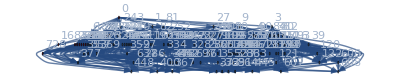

```mathematica
Graph[DeleteDuplicates[Flatten[Table[Table[DirectedEdge[k,child],{child,Flatten[allGraphs4[k,"children"]]}],{k,Keys[allGraphs4]}]]],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name",VertexStyle->Table[k->Red,{k,allGraphs4NullAtomKeys}]]
```

## Only level 4

```mathematica
DivideSpecial[a_,b_]:=If[b==0,0.5,a/b]
```

```mathematica
Monitor[
Table[
With[{list=Flatten[Table[Table[DivideSpecial[Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==3&]],Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==3&]]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
{Min[list],Max[list],Mean[list],Length[list]}]
,
{all,{allGraphs5}}
],Length[all]
]
```

{{0,1,0.5,17680}}

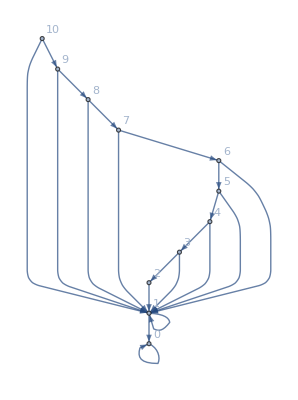

```mathematica
Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
```

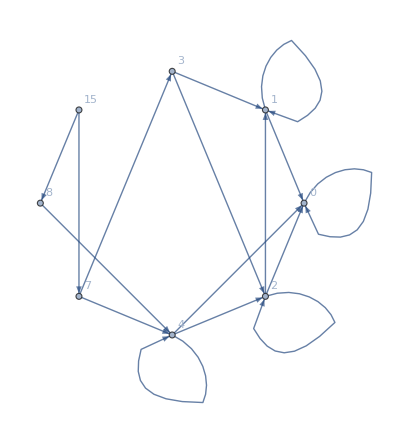

```mathematica
Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==2&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==2&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

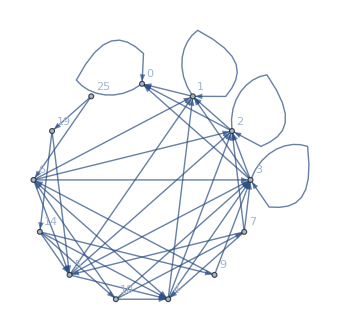

```mathematica
Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==3&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==3&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

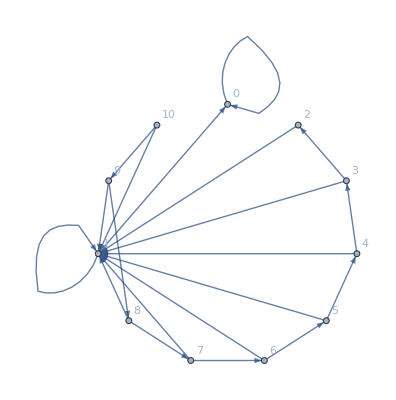

```mathematica
Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

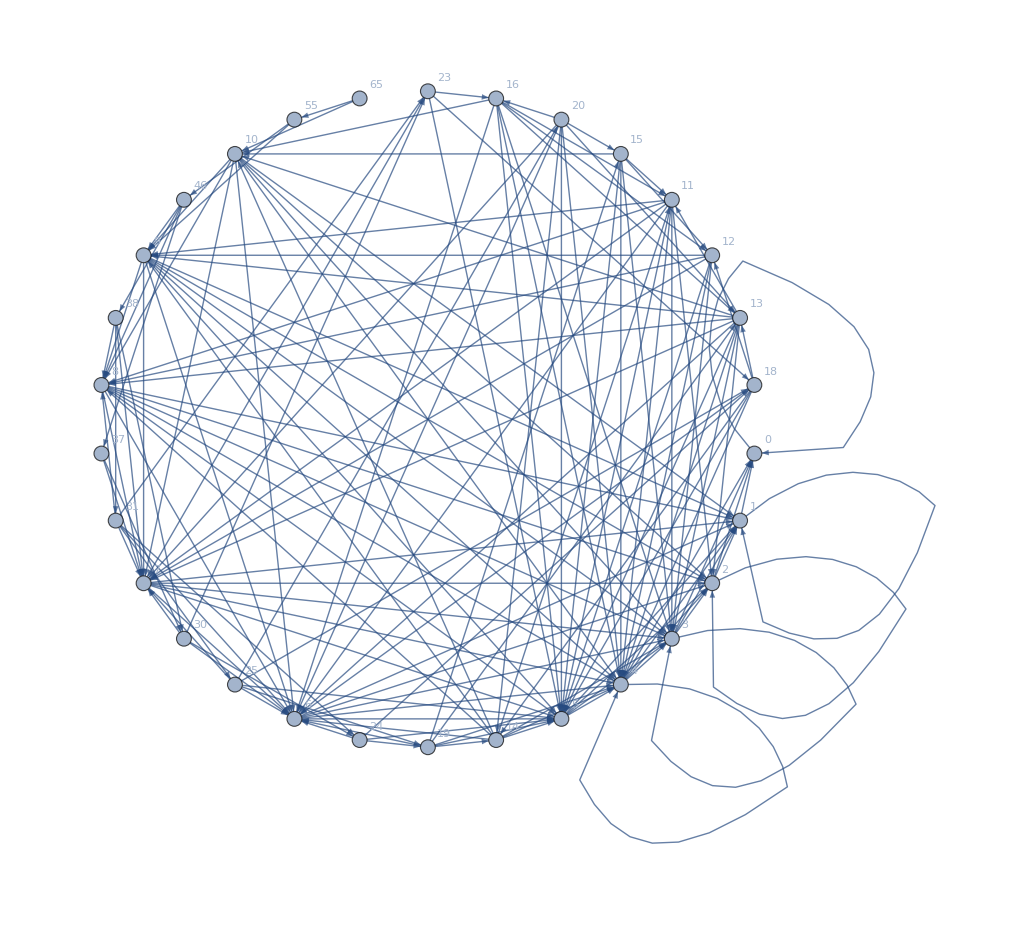

```mathematica
g6=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

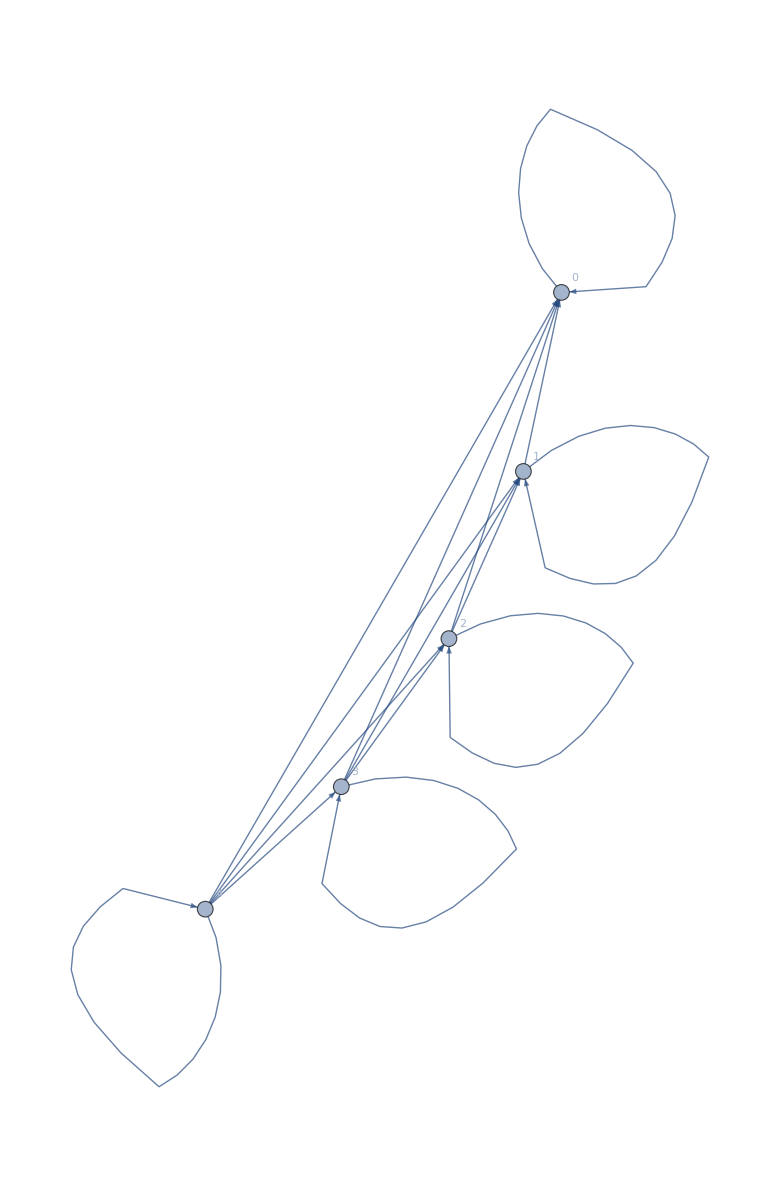

```mathematica
NeighborhoodGraph[g6,0,VertexLabels->"Name"]
```

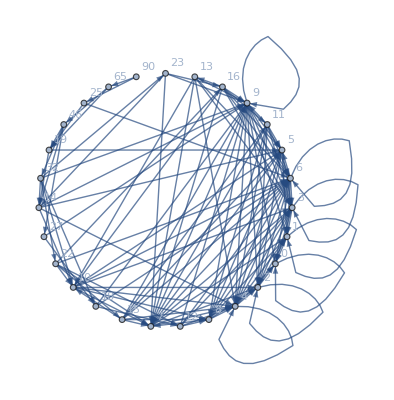

```mathematica
g63=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==3&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==3&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

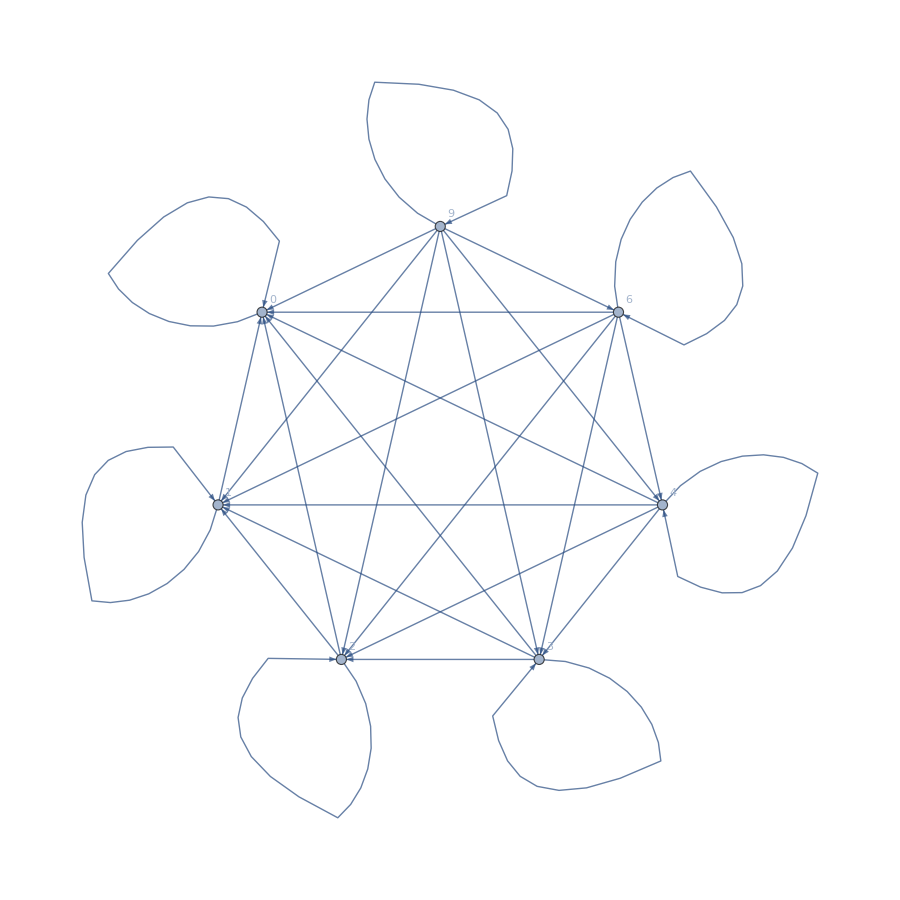

```mathematica
With[{g=NeighborhoodGraph[g63,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

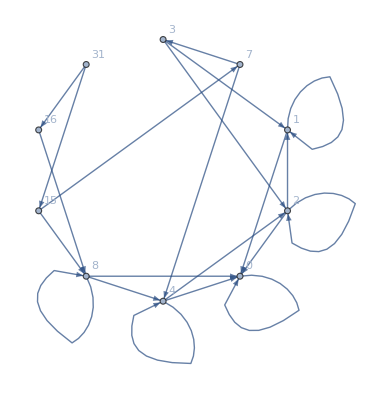

```mathematica
g62=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==2&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==2&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

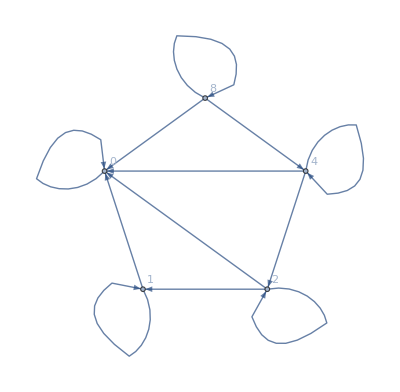

```mathematica
With[{g=NeighborhoodGraph[g62,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

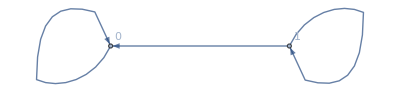

```mathematica
g61=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==1&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==1&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs6}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

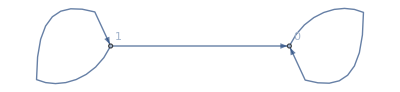

```mathematica
With[{g=NeighborhoodGraph[g61,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding", ]]
```

```mathematica
g54=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==4&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==4&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

-Graphics-

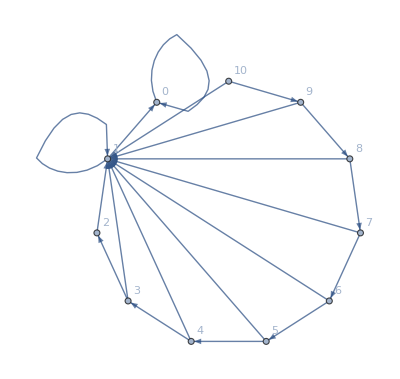

```mathematica
With[{g=NeighborhoodGraph[g54,1,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```

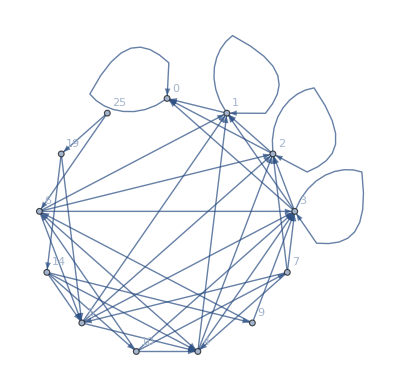

```mathematica
g53=Graph[Table[
With[{list=Flatten[Table[Table[Length[Select[ListofVars[all[k,"colofour"]],SymbolLevel[#]==3&]]->Length[Select[ListofVars[all[child,"colofour"]],SymbolLevel[#]==3&]],{child,Flatten[all[k,"children"]]}],{k,Keys[all]}]]},
list]
,
{all,{allGraphs5}}
]//First//DeleteDuplicates,VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

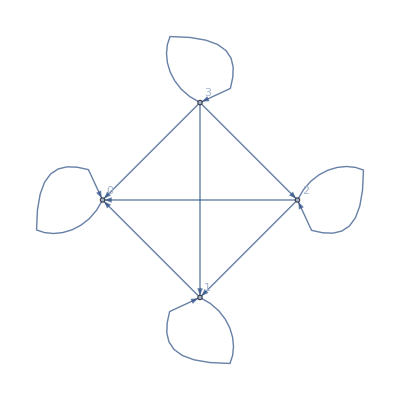

```mathematica
With[{g=NeighborhoodGraph[g53,0,VertexLabels->"Name"]},Graph[Sort[VertexList[g]],EdgeList[g],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]]
```